```mathematica
Get["new1through5Sequential.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward10[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Get["new1through5Sequential_20Kimura.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward20[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Get["new1through5Sequential_30Kimura.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward30[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Clear[fitVar, popMut,SourceNe, selectedNe, jumpSize, sigCutoff, α, VG, expectation, soln];
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.01;
VG =.000101;
expectation = 0.1;
```

```mathematica
soln = NDSolve[{D[f[x,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[x(1-x)f[x,t],x] + 1/2 D[x(1-x)f[x,t],{x,2}],
f[x,0]==Evaluate[PDF[TriangularDistribution[{(expectation - 0.001),(expectation + 0.001)},expectation],x]]} /. {Ne->selectedNe, Λ -> jumpSize, W->fitVar},
f,{x,0,1},{t,0,0.2},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.05}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg10_gen50.png",%24,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg10_gen50.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.1}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg10_gen100.png",%29,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg10_gen100.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.15}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg10_gen150.png",%34,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg10_gen150.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.05}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg20_gen50.png",%39,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg20_gen50.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.1}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg20_gen100.png",%44,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg20_gen100.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.15}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg20_gen150.png",%49,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg20_gen150.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.05}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.05}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg30_gen50.png",%54,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg30_gen50.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.1}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.1}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg30_gen100.png",%59,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg30_gen100.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.15}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.15}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg30_gen150.png",%64,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg30_gen150.png

```mathematica
(***************************************************************************************************************************)
```

```mathematica
Clear[fitVar, popMut,SourceNe, selectedNe, jumpSize, sigCutoff, α, VG, expectation, soln];
```

```mathematica
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.005;
VG =.000101;
expectation = 0.1;
```

```mathematica
soln = NDSolve[{D[f[x,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[x(1-x)f[x,t],x] + 1/2 D[x(1-x)f[x,t],{x,2}],
f[x,0]==Evaluate[PDF[TriangularDistribution[{(expectation - 0.001),(expectation + 0.001)},expectation],x]]} /. {Ne->selectedNe, Λ -> jumpSize, W->fitVar},
f,{x,0,1},{t,0,1},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.25}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg10_gen250.png",%89,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg10_gen250.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.5}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg10_gen500.png",%94,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg10_gen500.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.75}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg10_gen750.png",%99,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg10_gen750.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.25}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg20_gen250.png",%104,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg20_gen250.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.5}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg20_gen500.png",%109,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg20_gen500.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward20[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.75}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward20[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg20_gen750.png",%114,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg20_gen750.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.25}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.25}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg30_gen250.png",%119,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg30_gen250.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.5}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.5}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg30_gen500.png",%124,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg30_gen500.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.75}]];
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.75}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg30_gen750.png",%129,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg30_gen750.png

```mathematica
(******************************************************************************************************)
```

```mathematica
Clear[new]
```

```mathematica
Get["new1through5Sequential_50Kimura.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward50[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Clear[fitVar, popMut,SourceNe, selectedNe, jumpSize, sigCutoff, α, VG, expectation, soln];
```

```mathematica
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.001;
VG =.000101;
expectation = 0.1;
```

```mathematica
soln = NDSolve[{D[f[x,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[x(1-x)f[x,t],x] + 1/2 D[x(1-x)f[x,t],{x,2}],
f[x,0]==Evaluate[PDF[TriangularDistribution[{(expectation - 0.001),(expectation + 0.001)},expectation],x]]} /. {Ne->selectedNe, Λ -> jumpSize, W->fitVar},
f,{x,0,1},{t,0,0.05},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

```mathematica
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na1_geg10_gen20.png",%158,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na1_geg10_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na1_geg30_gen20.png",%162,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na1_geg30_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward50[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward50[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na1_geg50_gen20.png",%166,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na1_geg50_gen20.png

```mathematica
Clear[fitVar, popMut,SourceNe, selectedNe, jumpSize, sigCutoff, α, VG, expectation, soln];
```

```mathematica
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.005;
VG =.000101;
expectation = 0.1;
```

```mathematica
soln = NDSolve[{D[f[x,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[x(1-x)f[x,t],x] + 1/2 D[x(1-x)f[x,t],{x,2}],
f[x,0]==Evaluate[PDF[TriangularDistribution[{(expectation - 0.001),(expectation + 0.001)},expectation],x]]} /. {Ne->selectedNe, Λ -> jumpSize, W->fitVar},
f,{x,0,1},{t,0,0.05},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

```mathematica
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg10_gen20.png",%182,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg10_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg30_gen20.png",%186,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg30_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward50[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward50[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na5_geg50_gen20.png",%190,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na5_geg50_gen20.png

```mathematica
Clear[fitVar, popMut,SourceNe, selectedNe, jumpSize, sigCutoff, α, VG, expectation, soln];
```

```mathematica
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
α= 0.01;
VG =.000101;
expectation = 0.1;
```

```mathematica
soln = NDSolve[{D[f[x,t],t]== -(2 Ne α Λ / W) Exp[-2 Ne VG t / W] D[x(1-x)f[x,t],x] + 1/2 D[x(1-x)f[x,t],{x,2}],
f[x,0]==Evaluate[PDF[TriangularDistribution[{(expectation - 0.001),(expectation + 0.001)},expectation],x]]} /. {Ne->selectedNe, Λ -> jumpSize, W->fitVar},
f,{x,0,1},{t,0,0.05},MaxStepSize->.00025];
```

NDSolve::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::bcart: Warning: an insufficient number of boundary conditions have been specified for the direction of independent variable x. Artificial boundary effects may be present in the solution.

```mathematica
styles = Flatten@{Directive[ColorData[{"SouthwestColors",{1,7}}][1]],
Directive[ColorData[{"SouthwestColors",{1,7}}][2]],
Directive[ColorData[{"SouthwestColors",{1,7}}][3]],
Directive[ColorData[{"SouthwestColors",{1,7}}][4]],
Directive[ColorData[{"SouthwestColors",{1,7}}][5]],
Directive[ColorData[{"SouthwestColors",{1,7}}][6]],
Directive[Dashed, ColorData[{"SouthwestColors",{1,7}}][7]]};
```

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward10[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward10[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg10_gen20.png",%206,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg10_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward30[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward30[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg30_gen20.png",%210,"PNG"]
```

C:\Users\natha\Documents\GitHub\path_integral\2na10_geg30_gen20.png

```mathematica
Clear[funcs];
funcs  = Append[Evaluate[Table[SimplifiedHayward50[k]/. {x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02},{k,0, 5}]],
Evaluate[f[x,t] /.soln /. {x->y, t->0.02}]];
Plot[funcs,
{y,0,1},
PlotRangePadding->0.1,
ImageSize->500,
AspectRatio->1/2, 
PlotLabels->Append[Table[TextString[k],{k,0,5}],"NDSolve"],
PlotStyle-> styles,
PlotRange->{{0,1},{-10,10}}]

NMinimize[{Evaluate[SimplifiedHayward50[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> 0.02}], 0<= y <= 1},{y}]
```

-Graphics-

```mathematica
Export["C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg50_gen20.png",%214,"PNG"]
```

```mathematica
"C:\\Users\\natha\\Documents\\GitHub\\path_integral\\2na10_geg50_gen20.png"
```

```mathematica
(******************************************************************************************************)




Quit[]
```

```mathematica
Clear[new]
```

```mathematica
Get["new1through5Sequential_50Kimura.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward50[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
neutral = Kimura[x,y,t,50];
```

```mathematica
Clear[out];
out = {{"alpha","VG","start","thresh","totalP","Pdetected"}};
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
time = 0.05;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
out
```

{{alpha,VG,start,thresh,totalP,Pdetected}}

print[0.1]

0.984642

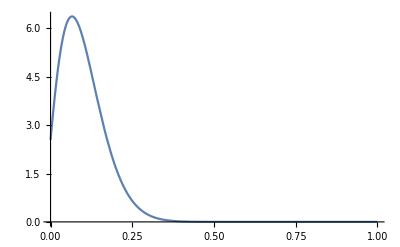

```mathematica
expectation = 0.1;
print[expectation]
neutAUC = NIntegrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}]
Plot[neutral/. {x->expectation, t->time}, {y,0,1}]
```

```mathematica
pNeutFix = 1- neutAUC
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, expectation+Ψ,1}]
```

0.0153581

0.439281-5.66309 Ψ+18.1249 Ψ^2+103.368 Ψ^3-991.541 Ψ^4+2000.65 Ψ^5+10738.4 Ψ^6-80152.2 Ψ^7+196838. Ψ^8+92630.5 Ψ^9-2.19779×10^6 Ψ^10+7.39137×10^6 Ψ^11-1.12916×10^7 Ψ^12-4.27129×10^6 Ψ^13+6.76178×10^7 Ψ^14-1.81593×10^8 Ψ^15+2.64193×10^8 Ψ^16-1.33364×10^8 Ψ^17-3.77779×10^8 Ψ^18+1.19487×10^9 Ψ^19-1.86424×10^9 Ψ^20+1.73983×10^9 Ψ^21-4.77487×10^8 Ψ^22-1.54419×10^9 Ψ^23+3.31798×10^9 Ψ^24-3.84834×10^9 Ψ^25+2.84903×10^9 Ψ^26-9.2206×10^8 Ψ^27-9.04526×10^8 Ψ^28+1.8629×10^9 Ψ^29-1.82357×10^9 Ψ^30+1.17753×10^9 Ψ^31-4.45488×10^8 Ψ^32-4.22205×10^7 Ψ^33+2.24935×10^8 Ψ^34-2.07583×10^8 Ψ^35+1.2144×10^8 Ψ^36-4.69427×10^7 Ψ^37+7.18223×10^6 Ψ^38+5.80341×10^6 Ψ^39-6.268×10^6 Ψ^40+3.61917×10^6 Ψ^41-1.51861×10^6 Ψ^42+489356. Ψ^43-119825. Ψ^44+20693.9 Ψ^45-1873.82 Ψ^46-139.298 Ψ^47+74.8073 Ψ^48-10.7386 Ψ^49+0.611024 Ψ^50

```mathematica
thresh = Solve[tmp == 1-sigCutoff && 0<Ψ<1, {Ψ}, Reals];
Print[thresh];
If[Length[thresh] != 1,Throw[{α, VG, thresh}]];
```

{{Ψ→0.192309}}

```mathematica
Ψ = Ψ /. thresh;
Print[Ψ];
```

{0.192309}

```mathematica
Ψ = Ψ[[1]]
```

0.192309

```mathematica
Do[Clear[totalP, Pdetected];
Print[α,VG];
totalP = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, 0,1}];
Pdetected = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, expectation+Ψ,1}];
Print[totalP, Pdetected];
Export[StringJoin["alpha",ToString[α], "_VG",ToString[VG],".csv"], {{α,VG,expectation,Ψ,totalP,Pdetected}}, "csv"],
{α, {0.0005,0.001,0.005, 0.01}},
{VG, {.101, .0101, .00101,.000101}}
]
```

0.00050.101

0.9848810.010206

0.00050.0101

0.9852830.0109237

0.00050.00101

0.9853810.0111732

0.00050.000101

0.9853930.0112029

0.0010.101

0.9851180.0104103

0.0010.0101

0.9859010.0119148

0.0010.00101

0.9860910.0124574

0.0010.000101

0.9861120.0125227

0.0050.101

0.9868830.0121846

0.0050.0101

0.9899940.0229376

0.0050.00101

0.9907840.028097

0.0050.000101

0.9908580.028746

0.010.101

0.9879320.0147411

0.010.0101

0.9477630.00218068

0.010.00101

0.9946740.0675159

0.010.000101

0.9947640.070118

```mathematica
(******************************************************************************************************)




Quit[]
```

```mathematica
Clear[new]
```

```mathematica
Get["new1through5Sequential_50Kimura.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward50[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
neutral = Kimura[x,y,t,50];
```

```mathematica
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
VG = 0.00101;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
```

```mathematica
expectation = 0.1;
print[expectation]
```

print[0.1]

```mathematica
Do[Clear[neutAUC, pNeutFix, tmp, thresh, Ψ, totalP, Pdetected];
Print[α,time];
neutAUC = NIntegrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}];
pNeutFix = 1- neutAUC;
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, expectation+Ψ,1}];
thresh = Solve[tmp == 1-sigCutoff && 0<Ψ<1, {Ψ}, Reals];
Print[thresh];
Ψ = Ψ /. thresh;
Ψ = Ψ[[1]];
Print[Ψ];
totalP = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, 0,1}];
Pdetected = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, expectation+Ψ,1}];
Print[totalP, Pdetected];
Export[StringJoin["alpha",ToString[α], "_time",ToString[time],".csv"], {{α,time,expectation,Ψ,totalP,Pdetected}}, "csv"],
{α, {0.0005,0.001,0.005, 0.01}},
{time, {.05, .1,.15}}
]
```

0.00050.05

{{Ψ→0.192309}}

0.192309

0.9853810.0111732

0.00050.1

{{Ψ→0.287261}}

0.287261

0.8840440.0117398

0.00050.15

{{Ψ→0.363427}}

0.363427

0.7686780.0121746

0.0010.05

{{Ψ→0.192309}}

0.192309

0.9860910.0124574

0.0010.1

{{Ψ→0.287261}}

0.287261

0.8896390.0137354

0.0010.15

{{Ψ→0.363427}}

0.363427

0.7797750.0147458

0.0050.05

{{Ψ→0.192309}}

0.192309

0.9907840.028097

0.0050.1

{{Ψ→0.287261}}

0.287261

0.9276490.0427238

0.0050.15

{{Ψ→0.363427}}

0.363427

0.8569970.0568879

0.010.05

{{Ψ→0.192309}}

0.192309

0.9946740.0675159

0.010.1

{{Ψ→0.287261}}

0.287261

0.9600030.131593

0.010.15

{{Ψ→0.363427}}

0.363427

0.9237820.198497

```mathematica
Do[Clear[neutAUC, pNeutFix, tmp, thresh, Ψ, totalP, Pdetected];
Print[α,time];
neutAUC = NIntegrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}];
pNeutFix = 1- neutAUC;
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, expectation+Ψ,1}];
thresh = Solve[tmp == 1-sigCutoff && 0<Ψ<1, {Ψ}, Reals];
Print[thresh];
Ψ = Ψ /. thresh;
Ψ = Ψ[[1]];
Print[Ψ];
totalP = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, 0,1}];
Pdetected = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, expectation+Ψ,1}];
Print[totalP, Pdetected];
Export[StringJoin["alpha",ToString[α], "_time",ToString[time],".csv"], {{α,time,expectation,Ψ,totalP,Pdetected}}, "csv"],
{α, {0.0005,0.001,0.005, 0.01}},
{time, {.2,.25}}
]
```

0.00050.2

{{Ψ→0.428846}}

0.428846

0.6732110.0125218

0.00050.25

{{Ψ→0.486736}}

0.486736

0.5978670.0128035

0.0010.2

{{Ψ→0.428846}}

0.428846

0.6887920.0155742

0.0010.25

{{Ψ→0.486736}}

0.486736

0.616920.0162595

0.0050.2

{{Ψ→0.428846}}

0.428846

0.799650.0702316

0.0050.25

{{Ψ→0.486736}}

0.486736

0.7552250.0823899

0.010.2

{{Ψ→0.428846}}

0.428846

0.8957840.261542

0.010.25

{{Ψ→0.486736}}

0.486736

0.8728960.316135

```mathematica
Clear[neutAUC, pNeutFix, tmp, thresh, Ψ, totalP, Pdetected];
```

```mathematica
neutral = Kimura[x,y,t,200];
```

```mathematica
α = 0.01
time = 0.025
```

0.01

0.025

```mathematica
0.03
```

0.03

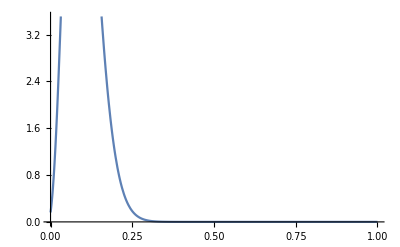

```mathematica
Plot[neutral/. {x->expectation, t->time}, {y,0,1}]
```

```mathematica
neutAUC = NIntegrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}]
pNeutFix = 1- neutAUC
```

0.999756

0.000244337

```mathematica
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, expectation+Ψ,1}]
thresh = Solve[tmp == 1-sigCutoff && 0<Ψ<1, {Ψ}, Reals]
```

6.19245×10^16-8.21392 Ψ+26.8728 Ψ^2+448.478 Ψ^3-3924.56 Ψ^4-6365.74 Ψ^5+227984. Ψ^6-905228. Ψ^7-3.80786×10^6 Ψ^8+4.90779×10^7 Ψ^9-1.41322×10^8 Ψ^10-5.31462×10^8 Ψ^11+5.81723×10^9 Ψ^12-1.76422×10^10 Ψ^13-2.05882×10^10 Ψ^14+3.81858×10^11 Ψ^15-1.44149×10^12 Ψ^16+1.37485×10^12 Ψ^17+1.12867×10^13 Ψ^18-6.2632×10^13 Ψ^19+1.45728×10^14 Ψ^20-1.68836×10^13 Ψ^21-1.13709×10^15 Ψ^22+4.41747×10^15 Ψ^23-8.30263×10^15 Ψ^24+1.4032×10^15 Ψ^25+4.38125×10^16 Ψ^26-1.54604×10^17 Ψ^27+2.86016×10^17 Ψ^28-1.96711×10^17 Ψ^29-6.09951×10^17 Ψ^30+2.67931×10^18 Ψ^31-6.31704×10^18 Ψ^32+1.3152×10^19 Ψ^33-3.61966×10^19 Ψ^34+1.36768×10^20 Ψ^35-5.39551×10^20 Ψ^36+1.97868×10^21 Ψ^37-6.72867×10^21 Ψ^38+2.15563×10^22 Ψ^39-6.55299×10^22 Ψ^40+1.88573×10^23 Ψ^41-5.10397×10^23 Ψ^42+1.29216×10^24 Ψ^43-3.05338×10^24 Ψ^44+6.75077×10^24 Ψ^45-1.40742×10^25 Ψ^46+2.80581×10^25 Ψ^47-5.45572×10^25 Ψ^48+1.0578×10^26 Ψ^49-2.08013×10^26 Ψ^50+4.16835×10^26 Ψ^51-8.44867×10^26 Ψ^52+1.71055×10^27 Ψ^53-3.42421×10^27 Ψ^54+6.74148×10^27 Ψ^55-1.30311×10^28 Ψ^56+2.47115×10^28 Ψ^57-4.58861×10^28 Ψ^58+8.31291×10^28 Ψ^59-1.46232×10^29 Ψ^60+2.48536×10^29 Ψ^61-4.06307×10^29 Ψ^62+6.36528×10^29 Ψ^63-9.5271×10^29 Ψ^64+1.35893×10^30 Ψ^65-1.8434×10^30 Ψ^66+2.3739×10^30 Ψ^67-2.89821×10^30 Ψ^68+3.3512×10^30 Ψ^69-3.66824×10^30 Ψ^70+3.80105×10^30 Ψ^71-3.73029×10^30 Ψ^72+3.47026×10^30 Ψ^73-3.06384×10^30 Ψ^74+2.57042×10^30 Ψ^75-2.05149×10^30 Ψ^76+1.5589×10^30 Ψ^77-1.12823×10^30 Ψ^78+7.7751×10^29 Ψ^79-5.09785×10^29 Ψ^80+3.17563×10^29 Ψ^81-1.87569×10^29 Ψ^82+1.04761×10^29 Ψ^83-5.51328×10^28 Ψ^84+2.72168×10^28 Ψ^85-1.25333×10^28 Ψ^86+5.34835×10^27 Ψ^87-2.09883×10^27 Ψ^88+7.50926×10^26 Ψ^89-2.42609×10^26 Ψ^90+7.00234×10^25 Ψ^91-1.78363×10^25 Ψ^92+3.95266×10^24 Ψ^93-7.48986×10^23 Ψ^94+1.18717×10^23 Ψ^95-1.52842×10^22 Ψ^96+1.53256×10^21 Ψ^97-1.12064×10^20 Ψ^98+5.30382×10^18 Ψ^99-1.21628×10^17 Ψ^100

{{Ψ→0.856203}}

```mathematica
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, 0, expectation+Ψ}]
thresh = Solve[tmp == sigCutoff - pNeutFix && 0<Ψ<1, {Ψ}, Reals]
```

0.542231+8.21392 Ψ-26.8728 Ψ^2-448.478 Ψ^3+3924.56 Ψ^4+6365.74 Ψ^5-227984. Ψ^6+905228. Ψ^7+3.80786×10^6 Ψ^8-4.90779×10^7 Ψ^9+1.41322×10^8 Ψ^10+5.31462×10^8 Ψ^11-5.81723×10^9 Ψ^12+1.76422×10^10 Ψ^13+2.05882×10^10 Ψ^14-3.81858×10^11 Ψ^15+1.44149×10^12 Ψ^16-1.37485×10^12 Ψ^17-1.12867×10^13 Ψ^18+6.2632×10^13 Ψ^19-1.45728×10^14 Ψ^20+1.68836×10^13 Ψ^21+1.13709×10^15 Ψ^22-4.41747×10^15 Ψ^23+8.30263×10^15 Ψ^24-1.4032×10^15 Ψ^25-4.38125×10^16 Ψ^26+1.54604×10^17 Ψ^27-2.86016×10^17 Ψ^28+1.96711×10^17 Ψ^29+6.09951×10^17 Ψ^30-2.67931×10^18 Ψ^31+6.31704×10^18 Ψ^32-1.3152×10^19 Ψ^33+3.61966×10^19 Ψ^34-1.36768×10^20 Ψ^35+5.39551×10^20 Ψ^36-1.97868×10^21 Ψ^37+6.72867×10^21 Ψ^38-2.15563×10^22 Ψ^39+6.55299×10^22 Ψ^40-1.88573×10^23 Ψ^41+5.10397×10^23 Ψ^42-1.29216×10^24 Ψ^43+3.05338×10^24 Ψ^44-6.75077×10^24 Ψ^45+1.40742×10^25 Ψ^46-2.80581×10^25 Ψ^47+5.45572×10^25 Ψ^48-1.0578×10^26 Ψ^49+2.08013×10^26 Ψ^50-4.16835×10^26 Ψ^51+8.44867×10^26 Ψ^52-1.71055×10^27 Ψ^53+3.42421×10^27 Ψ^54-6.74148×10^27 Ψ^55+1.30311×10^28 Ψ^56-2.47115×10^28 Ψ^57+4.58861×10^28 Ψ^58-8.31291×10^28 Ψ^59+1.46232×10^29 Ψ^60-2.48536×10^29 Ψ^61+4.06307×10^29 Ψ^62-6.36528×10^29 Ψ^63+9.5271×10^29 Ψ^64-1.35893×10^30 Ψ^65+1.8434×10^30 Ψ^66-2.3739×10^30 Ψ^67+2.89821×10^30 Ψ^68-3.3512×10^30 Ψ^69+3.66824×10^30 Ψ^70-3.80105×10^30 Ψ^71+3.73029×10^30 Ψ^72-3.47026×10^30 Ψ^73+3.06384×10^30 Ψ^74-2.57042×10^30 Ψ^75+2.05149×10^30 Ψ^76-1.5589×10^30 Ψ^77+1.12823×10^30 Ψ^78-7.7751×10^29 Ψ^79+5.09785×10^29 Ψ^80-3.17563×10^29 Ψ^81+1.87569×10^29 Ψ^82-1.04761×10^29 Ψ^83+5.51328×10^28 Ψ^84-2.72168×10^28 Ψ^85+1.25333×10^28 Ψ^86-5.34835×10^27 Ψ^87+2.09883×10^27 Ψ^88-7.50926×10^26 Ψ^89+2.42609×10^26 Ψ^90-7.00234×10^25 Ψ^91+1.78363×10^25 Ψ^92-3.95266×10^24 Ψ^93+7.48986×10^23 Ψ^94-1.18717×10^23 Ψ^95+1.52842×10^22 Ψ^96-1.53256×10^21 Ψ^97+1.12064×10^20 Ψ^98-5.30382×10^18 Ψ^99+1.21628×10^17 Ψ^100

{{Ψ→0.129578},{Ψ→0.927345}}

```mathematica
Print[thresh];
Ψ = Ψ /. thresh;
Ψ = Ψ[[1]];
Print[Ψ];
```

{{Ψ→0.785111}}

0.785111

```mathematica
Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, expectation+Ψ,1}]
```

-1.84303×10^8

```mathematica
NIntegrate[Evaluate[neutral/. {x->expectation, t->time}],{y, expectation+Ψ,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.997524778380687}. NIntegrate obtained -4.53887×10^-10 and 2.46089×10^-11 for the integral and error estimates.

-4.53887×10^-10

```mathematica
Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, 0,expectation+Ψ}]
```

841277.

```mathematica
NIntegrate[Evaluate[neutral/. {x->expectation, t->time}],{y, 0,expectation+Ψ}]
```

0.999969

```mathematica
expectation+Ψ
```

0.998949

```mathematica
totalP = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, 0,1}];
Pdetected = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, expectation+Ψ,1}];



(******************************************************************************************************)




Quit[]
```

{{Ψ→0.898949}}

0.898949

NIntegrate::inumr: The integrand SimplifiedHayward50[5] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

```mathematica
StringJoin["alpha",ToString[α], "_VG",ToString[VG],".csv"]
```

alpha0.01_VG0.101.csv

```mathematica
α = 0.01
VG = 0.101
```

0.01

0.101

```mathematica
Clear[expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected]
```

```mathematica
expectation = 0.1
print[expectation]
Plot[neutral/. {x->expectation, t->time}, {y,0,1}]
```

0.1

print[0.1]

-Graphics-

```mathematica
neutAUC = Integrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}]
pNeutFix = 1- neutAUC
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, Max[0,expectation-Ψ], Min[1,expectation+Ψ]}]
thresh = Solve[tmp == (sigCutoff - pNeutFix) && 0<Ψ<1, {Ψ}, Reals]
Print[thresh]
If[Length[thresh] != 1,Throw[{α, VG, thresh}]]
Ψ = Ψ /. thresh
Print[Ψ]
```

0.984637

0.0153635

-2.54376 Max[0.,0.1-1. Ψ]-55.7253 Max[0.,0.1-1. Ψ]^2+142.889 Max[0.,0.1-1. Ψ]^3+2936.82 Max[0.,0.1-1. Ψ]^4-21539.3 Max[0.,0.1-1. Ψ]^5+27332.8 Max[0.,0.1-1. Ψ]^6+347497. Max[0.,0.1-1. Ψ]^7-2.24474×10^6 Max[0.,0.1-1. Ψ]^8+5.97023×10^6 Max[0.,0.1-1. Ψ]^9-2.27865×10^6 Max[0.,0.1-1. Ψ]^10-4.2501×10^7 Max[0.,0.1-1. Ψ]^11+1.78861×10^8 Max[0.,0.1-1. Ψ]^12-3.86563×10^8 Max[0.,0.1-1. Ψ]^13+4.01284×10^8 Max[0.,0.1-1. Ψ]^14+3.63907×10^8 Max[0.,0.1-1. Ψ]^15-2.46609×10^9 Max[0.,0.1-1. Ψ]^16+5.56042×10^9 Max[0.,0.1-1. Ψ]^17-7.65534×10^9 Max[0.,0.1-1. Ψ]^18+5.6564×10^9 Max[0.,0.1-1. Ψ]^19+2.36867×10^9 Max[0.,0.1-1. Ψ]^20-1.46284×10^10 Max[0.,0.1-1. Ψ]^21+2.5322×10^10 Max[0.,0.1-1. Ψ]^22-2.78288×10^10 Max[0.,0.1-1. Ψ]^23+1.93972×10^10 Max[0.,0.1-1. Ψ]^24-3.51111×10^9 Max[0.,0.1-1. Ψ]^25-1.22125×10^10 Max[0.,0.1-1. Ψ]^26+2.09501×10^10 Max[0.,0.1-1. Ψ]^27-2.05493×10^10 Max[0.,0.1-1. Ψ]^28+1.3763×10^10 Max[0.,0.1-1. Ψ]^29-5.44964×10^9 Max[0.,0.1-1. Ψ]^30-6.23004×10^8 Max[0.,0.1-1. Ψ]^31+3.23888×10^9 Max[0.,0.1-1. Ψ]^32-3.22042×10^9 Max[0.,0.1-1. Ψ]^33+2.0666×10^9 Max[0.,0.1-1. Ψ]^34-9.07845×10^8 Max[0.,0.1-1. Ψ]^35+1.98402×10^8 Max[0.,0.1-1. Ψ]^36+8.37547×10^7 Max[0.,0.1-1. Ψ]^37-1.25575×10^8 Max[0.,0.1-1. Ψ]^38+8.55047×10^7 Max[0.,0.1-1. Ψ]^39-4.21168×10^7 Max[0.,0.1-1. Ψ]^40+1.63351×10^7 Max[0.,0.1-1. Ψ]^41-5.07746×10^6 Max[0.,0.1-1. Ψ]^42+1.24598×10^6 Max[0.,0.1-1. Ψ]^43-228413. Max[0.,0.1-1. Ψ]^44+26273.3 Max[0.,0.1-1. Ψ]^45-163.37 Max[0.,0.1-1. Ψ]^46-636.635 Max[0.,0.1-1. Ψ]^47+134.912 Max[0.,0.1-1. Ψ]^48-13.7937 Max[0.,0.1-1. Ψ]^49+0.611024 Max[0.,0.1-1. Ψ]^50+2.54376 Min[1.,0.1+Ψ]+55.7253 Min[1.,0.1+Ψ]^2-142.889 Min[1.,0.1+Ψ]^3-2936.82 Min[1.,0.1+Ψ]^4+21539.3 Min[1.,0.1+Ψ]^5-27332.8 Min[1.,0.1+Ψ]^6-347497. Min[1.,0.1+Ψ]^7+2.24474×10^6 Min[1.,0.1+Ψ]^8-5.97023×10^6 Min[1.,0.1+Ψ]^9+2.27865×10^6 Min[1.,0.1+Ψ]^10+4.2501×10^7 Min[1.,0.1+Ψ]^11-1.78861×10^8 Min[1.,0.1+Ψ]^12+3.86563×10^8 Min[1.,0.1+Ψ]^13-4.01284×10^8 Min[1.,0.1+Ψ]^14-3.63907×10^8 Min[1.,0.1+Ψ]^15+2.46609×10^9 Min[1.,0.1+Ψ]^16-5.56042×10^9 Min[1.,0.1+Ψ]^17+7.65534×10^9 Min[1.,0.1+Ψ]^18-5.6564×10^9 Min[1.,0.1+Ψ]^19-2.36867×10^9 Min[1.,0.1+Ψ]^20+1.46284×10^10 Min[1.,0.1+Ψ]^21-2.5322×10^10 Min[1.,0.1+Ψ]^22+2.78288×10^10 Min[1.,0.1+Ψ]^23-1.93972×10^10 Min[1.,0.1+Ψ]^24+3.51111×10^9 Min[1.,0.1+Ψ]^25+1.22125×10^10 Min[1.,0.1+Ψ]^26-2.09501×10^10 Min[1.,0.1+Ψ]^27+2.05493×10^10 Min[1.,0.1+Ψ]^28-1.3763×10^10 Min[1.,0.1+Ψ]^29+5.44964×10^9 Min[1.,0.1+Ψ]^30+6.23004×10^8 Min[1.,0.1+Ψ]^31-3.23888×10^9 Min[1.,0.1+Ψ]^32+3.22042×10^9 Min[1.,0.1+Ψ]^33-2.0666×10^9 Min[1.,0.1+Ψ]^34+9.07845×10^8 Min[1.,0.1+Ψ]^35-1.98402×10^8 Min[1.,0.1+Ψ]^36-8.37547×10^7 Min[1.,0.1+Ψ]^37+1.25575×10^8 Min[1.,0.1+Ψ]^38-8.55047×10^7 Min[1.,0.1+Ψ]^39+4.21168×10^7 Min[1.,0.1+Ψ]^40-1.63351×10^7 Min[1.,0.1+Ψ]^41+5.07746×10^6 Min[1.,0.1+Ψ]^42-1.24598×10^6 Min[1.,0.1+Ψ]^43+228413. Min[1.,0.1+Ψ]^44-26273.3 Min[1.,0.1+Ψ]^45+163.37 Min[1.,0.1+Ψ]^46+636.635 Min[1.,0.1+Ψ]^47-134.912 Min[1.,0.1+Ψ]^48+13.7937 Min[1.,0.1+Ψ]^49-0.611024 Min[1.,0.1+Ψ]^50

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{Ψ→0.192309}}

{{Ψ→0.192309}}

{0.192309}

{0.192309}

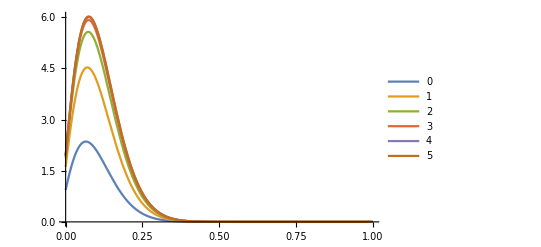

```mathematica
Plot[Evaluate[Table[SimplifiedHayward50[k]/. {x->expectation,t ->time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{k,0, 5}]],{y,0,1},PlotLegends->{Table[k,{k,0,5}]}]
```

```mathematica
NMinimize[{Evaluate[SimplifiedHayward50[5]/.{x->expectation,Ne->selectedNe, Λ -> jumpSize, W->fitVar,t -> time}], 0<= y <= 1},{y}]
```

{-4.52815×10^-12,{y→0.959352}}

```mathematica
totalP = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, 0,1}]
```

0.994674

```mathematica
Pdetectedplus = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Min[expectation+Ψ,1],1}]
```

0.0675159

```mathematica
Pnotdetected = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, Max[expectation-Ψ,0], Min[expectation+Ψ,1]}]
```

0.927158

```mathematica
Clear[α,VG]
```

```mathematica
Clear[expectation,neutAUC, pNeutFix, tmp,thresh,Ψ,totalP, Pdetected, Pnotdetected]
```

```mathematica
(******************************************************************************************************)




Quit[]
```

```mathematica
Get["new1through5Sequential.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward10[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
neutral = Kimura[x,y,t,10];
```

```mathematica
Clear[out];
out = {{"alpha","VG","start","thresh","totalP","Pdetected"}};
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
time = 0.05;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
out
```

{{alpha,VG,start,thresh,totalP,Pdetected}}

print[0.1]

0.976121

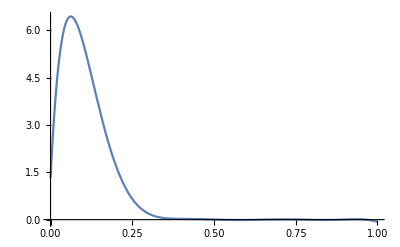

```mathematica
expectation = 0.1;
print[expectation]
neutAUC = NIntegrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}]
Plot[neutral/. {x->expectation, t->time}, {y,0,1}]
```

```mathematica
pNeutFix = 1- neutAUC
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, expectation+Ψ,1}]
```

0.0238788

0.437493-5.59074 Ψ+18.6248 Ψ^2+78.0151 Ψ^3-871.416 Ψ^4+3338.49 Ψ^5-7146.05 Ψ^6+9293.59 Ψ^7-7296.78 Ψ^8+3183.38 Ψ^9-592.668 Ψ^10

```mathematica
thresh = Solve[tmp == 1-sigCutoff && 0<Ψ<1, {Ψ}, Reals];
Print[thresh];
If[Length[thresh] != 1,Throw[{α, VG, thresh}]];
```

{{Ψ→0.186911},{Ψ→0.951086}}

Throw::nocatch: Uncaught Throw[{α,VG,{{Ψ→0.186911},{Ψ→0.951086}}}] returned to top level.

Hold[Throw[{α,VG,{{Ψ→0.186911},{Ψ→0.951086}}}]]

```mathematica
Ψ = Ψ /. thresh;
Print[Ψ];
```

{0.186911,0.951086}

```mathematica
Ψ = Ψ[[1]]
```

0.186911

```mathematica
Do[Clear[totalP, Pdetected];
Print[α,VG];
totalP = NIntegrate[SimplifiedHayward10[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, 0,1}];
Pdetected = NIntegrate[SimplifiedHayward10[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, expectation+Ψ,1}];
Export[StringJoin["alpha",ToString[α], "_VG",ToString[VG],".csv"], {{α,VG,expectation,Ψ,totalP,Pdetected}}, "csv"],
{α, {0.0005,0.001,0.005, 0.01}},
{VG, {.101, .0101, .00101,.000101}}
]
```

0.00050.101

0.00050.0101

0.00050.00101

0.00050.000101

0.0010.101

0.0010.0101

0.0010.00101

0.0010.000101

0.0050.101

0.0050.0101

0.0050.00101

0.0050.000101

0.010.101

0.010.0101

0.010.00101

0.010.000101

```mathematica
Flatten[Table[{x,y,f[x,y]},{x,0,1,.1},{y,0,1.1}],1]
```

{{0.,0,f[0.,0]},{0.,1,f[0.,1]},{0.1,0,f[0.1,0]},{0.1,1,f[0.1,1]},{0.2,0,f[0.2,0]},{0.2,1,f[0.2,1]},{0.3,0,f[0.3,0]},{0.3,1,f[0.3,1]},{0.4,0,f[0.4,0]},{0.4,1,f[0.4,1]},{0.5,0,f[0.5,0]},{0.5,1,f[0.5,1]},{0.6,0,f[0.6,0]},{0.6,1,f[0.6,1]},{0.7,0,f[0.7,0]},{0.7,1,f[0.7,1]},{0.8,0,f[0.8,0]},{0.8,1,f[0.8,1]},{0.9,0,f[0.9,0]},{0.9,1,f[0.9,1]},{1.,0,f[1.,0]},{1.,1,f[1.,1]}}

```mathematica
α = 0.001
VG = 0.00101 
Pdetected = 0.5
```

0.001

0.00101

0.5

```mathematica
{{α,VG,expectation,Ψ,totalP,Pdetected}}
```

{{0.001,0.00101,0.1,0.186911,0.977303,0.5}}

```mathematica
Export[StringJoin["alpha",ToString[α], "_VG",ToString[VG],".csv"], {{α,VG,expectation,Ψ,totalP,Pdetected}}, "csv"]
```

alpha0.001_VG0.00101.csv

```mathematica
Table[ NIntegrate[SimplifiedHayward10[3]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, 0,1}],
{α, {0.0005,0.001,0.005, 0.01}},
{VG, {.101, .0101, .00101,.000101}}
]
```

```mathematica
(******************************************************************************************************)




Quit[]
```

```mathematica
Clear[new]
```

```mathematica
Get["new1through5Sequential_50Kimura.m"]
```

```mathematica
For[k = 0, k ≤5,k++,
SimplifiedHayward50[k] = Exp[(2 Ne α Λ / W)(y Exp[-2 Ne VG t / W] - x)]* Sum[(2 Ne^2 α Λ / W^2)^j * new[j], {j, 0, k}]
]
```

```mathematica
Clear[new]
```

```mathematica
Kimura[x_,y_,t_,n_]:= Module[{m},Sum[4*(2*m+1)*x*(1-x)/(m*(m+1))*GegenbauerC[m-1,3/2,1-2*x]*GegenbauerC[m-1,3/2,1-2*y]*Exp[-1/2*m*(m+1)*t],{m,1,n}]
]
neutral = Kimura[x,y,t,50];
```

```mathematica
time = 0.05;
fitVar = 1;
popMut = 0.5;
SourceNe = 20000;
VG = 0.00101;
selectedNe = 500;
jumpSize = 1;
sigCutoff = 0.99;
```

```mathematica
Do[Clear[neutAUC, pNeutFix, tmp, thresh, Ψ, totalP, Pdetected];
Print[α,expectation];
neutAUC = NIntegrate[Evaluate[neutral/. {x->expectation, t->time}], {y,0,1}];
pNeutFix = 1- neutAUC;
tmp = Integrate[Evaluate[neutral/. {x->expectation, t->time}],{y, expectation+Ψ,1}];
thresh = Solve[tmp == 1-sigCutoff && 0<Ψ<1, {Ψ}, Reals];
Print[thresh];
Ψ = Ψ /. thresh;
Ψ = Ψ[[1]];
Print[Ψ];
totalP = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, 0,1}];
Pdetected = NIntegrate[SimplifiedHayward50[5]/.{x->expectation,t -> time, Ne->selectedNe, Λ -> jumpSize, W->fitVar},{y, expectation+Ψ,1}];
Print[totalP, Pdetected];
Export[StringJoin["alpha",ToString[α], "_start",ToString[expectation],".csv"], {{α,expectation,Ψ,totalP,Pdetected}}, "csv"],
{α, {0.005, 0.01}},
{expectation, {0.025,.05, .1,.15,.2}}
]
```

0.0050.025

{{Ψ→0.123882}}

0.123882

0.6817150.0203554

0.0050.05

{{Ψ→0.154512}}

0.154512

0.9004460.0236342

0.0050.1

{{Ψ→0.192309}}

0.192309

0.9907840.028097

0.0050.15

{{Ψ→0.216512}}

0.216512

0.9992120.0312841

0.0050.2

{{Ψ→0.23324}}

0.23324

0.9999380.0335953

0.010.025

{{Ψ→0.123882}}

0.123882

0.7226820.0383886

0.010.05

{{Ψ→0.154512}}

0.154512

0.9243940.0499938

0.010.1

{{Ψ→0.192309}}

0.192309

0.9946740.0675159

0.010.15

{{Ψ→0.216512}}

0.216512

0.9996490.080869

0.010.2

{{Ψ→0.23324}}

0.23324

0.9999750.0909478